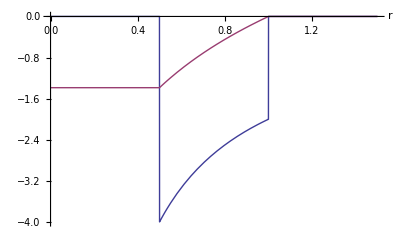

```mathematica
Needs["PlotLegends`"];
(* Radial potential and field *)
g1 =Plot[{Piecewise[{{0,r<0.5},{-2/r,r>0.5 && r < 1}}],Piecewise[{{-2Log[2],r<0.5},{2Log[r],r>0.5 && r < 1}}]},{r,0,1.5},Exclusions->None,AxesLabel->Automatic,PlotRangePadding->.1,PlotLegend->{"E_r","ϕ"},LegendShadow->None,LegendSize->{0.4,0.3},LegendPosition->{0.4,-0.5}]
```

```mathematica
Export["/Users/sgess/Desktop/FACET/hollow_chan/figures/fields.pdf",g1,ImageResolution->600];
```

```mathematica
(*s=NDSolve[{(2+2Log[r[ξ]])r''[ξ]+(r'[ξ])^2/r[ξ] == 0,r[0]==1,r'[0]==-0.46191},r,{ξ,0,1}]*)
s=NDSolve[{(2+2Log[r[ξ]])r[ξ]*r''[ξ]+(r'[ξ])^2 == 0,r[0]==1,r'[0]==-0.461},r,{ξ,0,1}]
```

{{r→InterpolatingFunction[{{0.,1.}},<>]}}

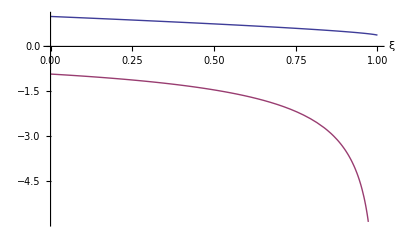

```mathematica
Needs["PlotLegends`"];g2=Plot[{Evaluate[r[ξ]/.s],Evaluate[2r'[ξ]/r[ξ]/.s]},{ξ,0,1},AxesLabel->Automatic,PlotLegend->{"r_s","E_z"},LegendShadow->None,LegendSize->{0.4,0.3},LegendPosition->{-0.8,-0.6}]
```

```mathematica
Export["/Users/sgess/Desktop/FACET/hollow_chan/figures/sheath.pdf",g2,ImageResolution->600];
```